## Dataset Preparation

```mathematica
(*Define number of dat points and clusters*)
nNormal=100;
nOut=1
nClust=3;
nX=nNormal*nClust+nOut;
(*Initialize data points and random initial means*)
randomClust[a_,b_,n_]:=RandomVariate[NormalDistribution[a,b],{n,2}]
matX=Join[randomClust[0,5,nNormal],randomClust[5,5,nNormal],randomClust[10,5,nNormal],RandomReal[{90,100},{nOut,2}]];
```

1

## K-mean

```mathematica
(*Random initial means*)
mean=Sort[RandomReal[{0,10},{nClust,2}]];
(*L-2 Norm*)
dist[a_,b_]:=Norm[a-b,2]
(*Position of minimum in l_List*)
belong2[l_List]:=Position[l,Min[l]]
(*Select all points in a cluster*)
sele[iCluster_]:=Select[matX,clusters[#]==iCluster&]
meanTemp={};
(*Number of iterations*)
iter=0;
While[meanTemp!=mean(*Stop when positions  of cluster means do not change*),
(*Distance b/w a data points and means*)
distances=Table[dist[matX[[iX]],mean[[iM]]],{iX,1,nX},{iM,1,nClust}];
(*Which cluster does each point belong to*)
clustering=Flatten[belong2/@distances];
clusters=AssociationThread[matX,clustering];
meanTemp=mean;
(*Update means with new cluster means*)
mean=Mean/@sele/@Range[1,nClust];
iter=iter+1;]
iter
```

21

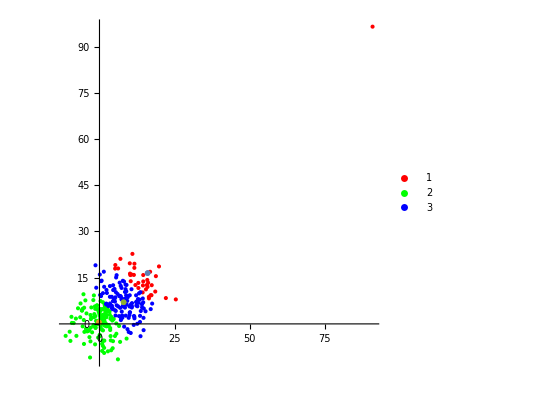

```mathematica
Show[ListPlot[sele/@Range[1,nClust],PlotLegends->Automatic,PlotStyle->{Red,Green,Blue}],ListPlot[{#}&/@mean,PlotMarkers->{Red,Green,Blue}],PlotRange->All,AspectRatio->1]
```

## K-median

```mathematica
(*Random initial medians*)
median=Sort[RandomSample[matX,3]];
(*L-1 Norm*)
dist[a_,b_]:=Norm[a-b,1]
(*Position of minimum in l_List*)
belong2[l_List]:=Position[l,Min[l]]
(*Select all points in a cluster*)
sele[iCluster_]:=Select[matX,clusters[#]==iCluster&]
medianTemp={};
(*Number of iterations*)
iter=0;
While[medianTemp!=median(*Stop when positions  of cluster medians do not change*),
(*Distance b/w a data points and medians*)
distances=Table[dist[matX[[iX]],median[[iM]]],{iX,1,nX},{iM,1,nClust}];
(*Which cluster does each point belong to*)
clustering=Flatten[belong2/@distances];
clusters=AssociationThread[matX,clustering];
medianTemp=median;
(*Update means with new cluster medians*)
median=Median/@sele/@Range[1,nClust];
iter=iter+1;]
iter
```

10

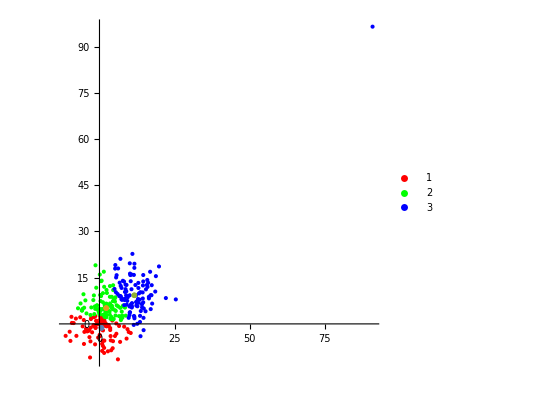

```mathematica
Show[ListPlot[sele/@Range[1,nClust],PlotLegends->Automatic,PlotStyle->{Red,Green,Blue}],ListPlot[{#}&/@median,PlotMarkers->{Red,Green,Blue}],PlotRange->All,AspectRatio->1]
```

```mathematica
mean
median
```

{{8.76684,10.0544},{2.28839,5.2001},{6.70896,2.59106}}

{{3.61948,7.56589},{9.11473,9.56832},{5.20192,1.9966}}

```mathematica
Mean/@sele/@Range[1,nClust]
Median/@sele/@Range[1,nClust]
```

{{3.34211,7.2071},{9.62427,10.0383},{5.16684,2.09291}}

{{3.61948,7.56589},{9.11473,9.56832},{5.20192,1.9966}}

```mathematica
Print@OutputForm@StringRiffle[SortBy[StringSplit["0K-1999K/ 10909K-10950K/ 10950K-12748K/ 12748K-14748K/ 14748K-16748K/ 16748K-16777K/ 16777K-18777K/ 1999K-3999K/ 3999K-5999K/ 5999K-6999K/ 6999K-8999K/ 8999K-9870K/ 9870K-10909K/ 18777K-20777K/ 20777K-22777K/ 22777K-24777K/ 24777K-26531K/ 26531K-28531K/ 28531K-30531K/"],ToExpression[StringReplace[#,x:DigitCharacter..~~"K"~~"-"~~__->x]]&]]
```

0K-1999K/ 1999K-3999K/ 3999K-5999K/ 5999K-6999K/ 6999K-8999K/ 8999K-9870K/ 9870K-10909K/ 10909K-10950K/ 10950K-12748K/ 12748K-14748K/ 14748K-16748K/ 16748K-16777K/ 16777K-18777K/ 18777K-20777K/ 20777K-22777K/ 22777K-24777K/ 24777K-26531K/ 26531K-28531K/ 28531K-30531K/

```mathematica
Sort[StringReplace[x:DigitCharacter..~~"K"~~"-"~~__->x]/@StringSplit["0K-1999K/ 10909K-10950K/ 10950K-12748K/ 12748K-14748K/ 14748K-16748K/ 16748K-16777K/ 16777K-18777K/ 1999K-3999K/ 3999K-5999K/ 5999K-6999K/ 6999K-8999K/ 8999K-9870K/ 9870K-10909K/ 18777K-20777K/ 20777K-22777K/ 22777K-24777K/ 24777K-26531K/ 26531K-28531K/ 28531K-30531K/"]]
```

{0,10909,10950,12748,14748,16748,16777,18777,1999,20777,22777,24777,26531,28531,3999,5999,6999,8999,9870}

```mathematica
StringReplace[x:DigitCharacter..~~"K"~~"-"~~__->ToExpression[x]]/@StringSplit["0K-1999K/ 10909K-10950K/ 10950K-12748K/ 12748K-14748K/ 14748K-16748K/ 16748K-16777K/ 16777K-18777K/ 1999K-3999K/ 3999K-5999K/ 5999K-6999K/ 6999K-8999K/ 8999K-9870K/ 9870K-10909K/ 18777K-20777K/ 20777K-22777K/ 22777K-24777K/ 24777K-26531K/ 26531K-28531K/ 28531K-30531K/"]
```

{0,10909,10950,12748,14748,16748,16777,1999,3999,5999,6999,8999,9870,18777,20777,22777,24777,26531,28531}

```mathematica
Sort[{"0","10909","10950","12748","14748","16748","16777","18777","1999","20777","22777","24777","26531","28531","3999","5999","6999","8999","9870"}]
```

{0,10909,10950,12748,14748,16748,16777,18777,1999,20777,22777,24777,26531,28531,3999,5999,6999,8999,9870}